# Chemical Reaction Networks: the well-mixed mass-action deterministic continuous case for large (bulk) volumes

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

## David Soloveichik’s simulator package

If they are not already present in this notebook’s directory, you need to download the three files CRNSimulator.m, CRNSimulatorExtensions.m, and CRNSimulatorSSA.m from http://users.ece.utexas.edu/~soloveichik/crnsimulator.html and place them in the same directory as this notebook.  Warning: Last year’s class used the June 5, 2016 version CRNSimulator.m and January 3, 2017 version of CRNSimulatorSSA.m.  This year, we are using the latest versions: January 8, 2022 and March 16, 2021 respectively.  Some backwards incompatibilities were introduced, so be careful if you have code from past years (e.g. if you are the TA).

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
```

See basic documentation for the key functions, e.g:

```mathematica
?SimulateRxnsys
```

```mathematica
?RxnsysToOdesys
```

```mathematica
?SpeciesInRxnsys
```

For this package, a model reaction system consists of an unordered set of reactions and concentration statements.  Species names are simply Mathematica symbols (i.e. variables) that have no values or rules assigned to them.  Thus, for example, the symbols “C” and “D” and “N” and “I” should not be used as species names, because Mathematica has built-in meanings for these terms.  Similarly, if your code assigns e.g. x=17, then “x” cannot be used as a species name unless you first execute Clear[x].  Once a reaction system has been defined, SimulateRxnsys[ ] builds the corresponding ODE equations for continuous deterministic mass-action chemical kinetics and performs the simulation.  The numerical integration of ODEs in Mathematica is an interpolating function that can be queried to obtain the value at a particular point.  These functions can be passed to Plot[ ] to draw the results, or they can be used in others ways to interrogate the simulation’s results.

What follows are a few annotated examples.

### Simple Chemical Reaction Networks

We explore a few networks, just to illustrate how easy it is to play.

The rxn[ ] statement indicates the reactants, products, and rate constant.  Note that when a rxn[ ] statement is displayed, it gets printed such that it looks more like you would expect.

Note that when a reaction has no products, that is indicated by placing a constant where products would be listed -- in this case 0, but any other constant would give the same result.  Similarly, for zero-order reactions that consume no reactants, a constant is placed in the reactant slot.

```mathematica
Clear[F,R];
tmax=8;
```

```mathematica
rsys={rxn[F,0,1],conc[F,1]}
```

{  F⟶^10,conc[F,1]}

```mathematica
rsys//FullForm
```

List[rxn[F,0,1],conc[F,1]]

```mathematica
sol=SimulateRxnsys[rsys,tmax]
```

{F→InterpolatingFunction[…]}

```mathematica
F[4.3]/.sol
```

0.0135685

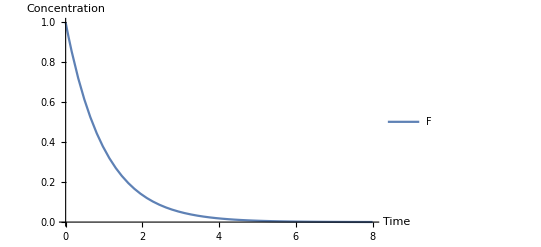

```mathematica
sol=SimulateRxnsys[{rxn[F,0,1],conc[F,1]},tmax];
Plot[F[t]/.sol,{t,0,tmax},PlotRange->{0,All},AxesLabel->{Time,Concentration},PlotLegends->{F}]
```

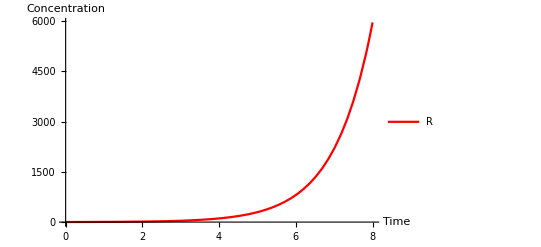

```mathematica
sol=SimulateRxnsys[{rxn[R,2R,1],conc[R,2]},tmax];
Plot[R[t]/.sol,{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red}},AxesLabel->{Time,Concentration},PlotLegends->{R}]
```

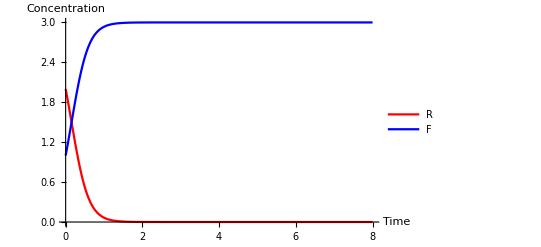

```mathematica
sol=SimulateRxnsys[{rxn[R+F,2F,1.5],conc[R,2],conc[F,1]},tmax];
Plot[Evaluate[{R[t],F[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Blue}},AxesLabel->{Time,Concentration},PlotLegends->{R,F}]
```

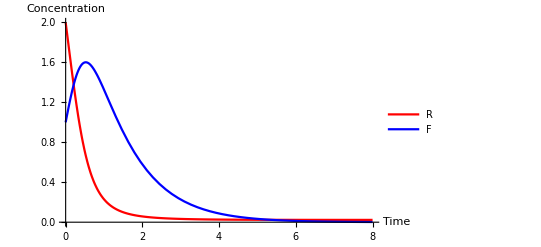

```mathematica
sol=SimulateRxnsys[{rxn[F,0,1],rxn[R+F,2F,1.5],conc[R,2],conc[F,1]},tmax];
Plot[Evaluate[{R[t],F[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Blue}},AxesLabel->{Time,Concentration},PlotLegends->{R,F}]
```

An aside about the Evaluate[ ] statement: A common confusion in Mathematica arises from functions and symbols that use the HoldFirst or HoldAll attribute, such as Plot[ ].  What this means is that the arguments are passed to the function symbolically “as-is”, without evaluating them automatically -- then the function itself can evaluate them if and as it wishes.  Plot[ ], for example, looks at the symbolic form of its input to determine how to assign colors, for example: if the input is a list of three things, use three colors, etc.  The exception to Hold is if the input is wrapped in Evaluate[ ], in which case it does get evaluated before being passed to the function.  That helps in this case, because rather than being a ReplaceAll[ ] expression, the input will now be a list containing the two functions to be plotted.

```mathematica
??Plot
```

### Predator-Prey

The classical Lotka-Volterra model for ecological dynamics can be represented as a CRN with three reactions.

```mathematica
rsys={
rxn[F,0,1],
rxn[R,2R,1],
rxn[R+F,2F,1.5],
conc[R,2],
conc[F,1]
}
```

{  F⟶^10,  R⟶^12 R,  F+R⟶^1.52 F,conc[R,2],conc[F,1]}

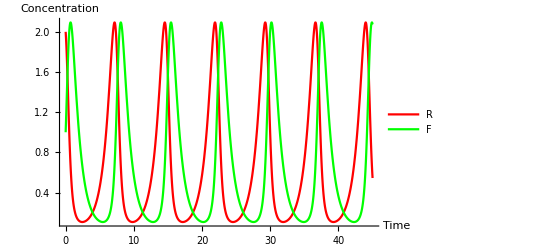

```mathematica
tmax=45;sol=SimulateRxnsys[rsys,tmax];Plot[Evaluate[{R[t],F[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}},AxesLabel->{Time,Concentration},PlotLegends->{R,F}]
```

You can set up the same predator-prey ODEs by hand if you like; this is what SimulateRxnsys is doing under the hood automatically.

```mathematica
tmax=45;
sol=NDSolve[{
R'[t]== R[t]-1.5*R[t]*F[t],
F'[t]==1.5*R[t]*F[t]-F[t],
R[0]==2,F[0]==1},
{R,F},{t,0,tmax}]
```

{{R→InterpolatingFunction[…],F→InterpolatingFunction[…]}}

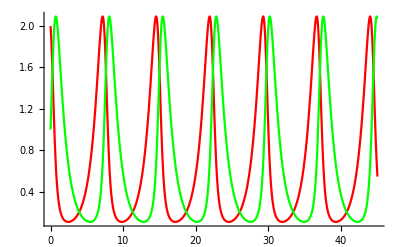

```mathematica
Plot[Evaluate[{R[t],F[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}}]
```

```mathematica
RxnsysToOdesys[rsys]
```

{F'[t]==-F[t]+1.5 F[t] R[t],R'[t]==R[t]-1.5 F[t] R[t],R[0]==2,F[0]==1}

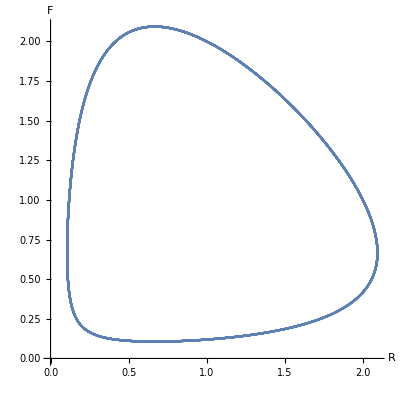

```mathematica
ParametricPlot[Evaluate[{R[t],F[t]}/.sol],{t,0,tmax},AxesLabel->{R,F}]
```

```mathematica
sols=Table[
NDSolve[{
R'[t]== R[t]-1.5*R[t]*F[t],
F'[t]==1.5*R[t]*F[t]-F[t],
R[0]==Rinit,F[0]==1},
{R,F},{t,0,tmax}],
{Rinit,0,3,0.1}];
```

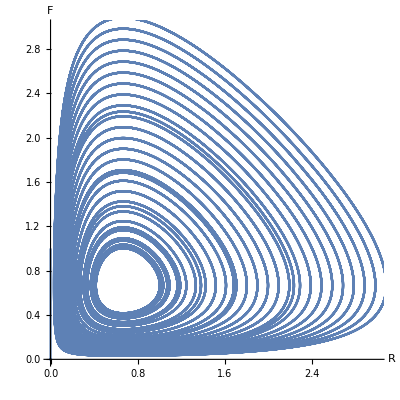

```mathematica
Show@@(With[{fncs={R[t],F[t]}/.#},ParametricPlot[fncs,{t,0,tmax},PlotRange->{{0,3},{0,3}},AxesLabel->{R,F}]]&/@sols)
```

### Considerations about reversible reactions and units of time and concentration

It is important to understand that the user is responsible for keeping track of units.  In the example below, the forward rate constants for bimolecular reactions are 1.5*10^6 /M/s, while the reverse reaction is 10 /s.  The unimolecular reactions are 3 x10^-4 /s.  The initial concentrations are 10^-9 M, i.e. 10 nM.  Time is expressed in seconds, so the simulation follows 2 hours of dynamics.

We also introduce here the revrxn[ ] statement, which is merely a shorthand for both the forward reaction and the reverse reaction simultaneously.  Because you might want to think of such reactions as inherently paired, the simulator leaves them as you wrote them... but for simulations they are identical to have two separate reactions.  ExpandRevrxns[ ] explicitly puts them in that form if you prefer it.

```mathematica
rsys={
revrxn[a+b,b+b,1.5 10^6,10],
revrxn[b+c,c+c,1.5 10^6,10],
revrxn[c+a,a+a,1.5 10^6,10],
rxn[a,0,0.0003],rxn[b,0,0.0003],rxn[c,0,0.0003],
conc[{a,c},10^-8]
}
```

{  a+b⟷_10^(1.5×10^6)2 b,  b+c⟷_10^(1.5×10^6)2 c,  a+c⟷_10^(1.5×10^6)2 a,  a⟶^0.00030,  b⟶^0.00030,  c⟶^0.00030,conc[{a,c},1/100000000]}

```mathematica
ExpandRevrxns[rsys]
```

{  a+b⟶^(1.5×10^6)2 b,  2 b⟶^10a+b,  b+c⟶^(1.5×10^6)2 c,  2 c⟶^10b+c,  a+c⟶^(1.5×10^6)2 a,  2 a⟶^10a+c,  a⟶^0.00030,  b⟶^0.00030,  c⟶^0.00030,conc[{a,c},1/100000000]}

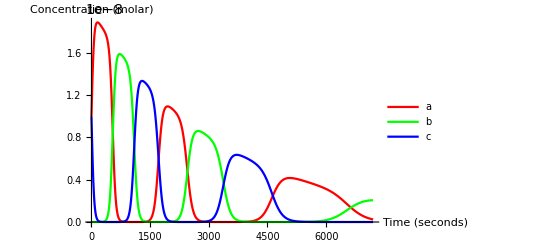

```mathematica
tmax=2*60*60;
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t],b[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}},AxesLabel->{"Time (seconds)","Concentration (molar)"},PlotLegends->{a,b,c}]
```

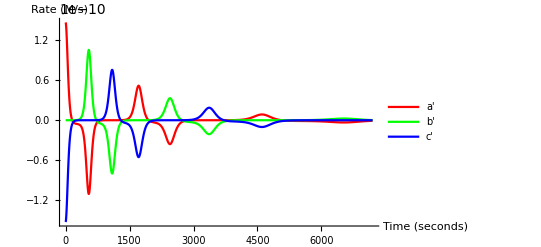

```mathematica
plotter={a'[t],b'[t],c'[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green},{Blue}},AxesLabel->{"Time (seconds)","Rate (M/s)"},PlotLegends->{a',b',c'}]
```

It is useful to be able to automate the analysis of CRN trajectories.  For example, we can easily get the peaks of each oscillation cycle.  Or the times at which a concentration hits some target can be found by numerically minimizing the squared difference of the concentration from the target.

```mathematica
a[500]/.sol
```

1.31287×10^-8

```mathematica
(* the 10^9 factor brings the numerical values of the concentrations (now nM rather than M) in a range that leads to better numerical stability *)
FindMaximum[10^9 a[t]/.sol,{t,10,15}]
```

{18.8897,{t→155.073}}

```mathematica
(* don't worry about the out-of-bounds invocations of the interpolating function *)
atops=Table[t/.Last[FindMaximum[10^9a[t]/.sol,{t,t0-50,t0+50}]],{t0,100,7000,100}];
```

InterpolatingFunction::dmval: Input value {-52.7297} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-256.24} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-18.6992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
atops=Union[Round[#,0.1]&/@atops]
```

{155.1,1947.2,5070.5}

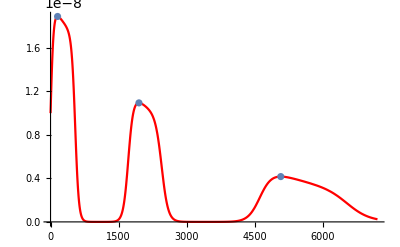

```mathematica
Show[Plot[a[t]/.sol,{t,0,tmax},PlotStyle->Red],ListPlot[{#,a[#]/.sol}&/@atops]]
```

```mathematica
NMaximize[{a[t]/.sol,t>0,t<tmax},t]
```

{1.88897×10^-8,{t→155.073}}

```mathematica
(* where does it hit 1 nM ? *)
a1nms=Table[t/.Last[FindMinimum[(10^9a[t]-1)^2/.sol,{t,t0-50,t0+50}]],{t0,100,7000,100}];
```

InterpolatingFunction::dmval: Input value {-6.07585} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-40.7326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-19.3136} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
at1nms=Union[Round[#,0.1]&/@a1nms]
```

{-9.9,654.7,1584.,2605.6,4448.5,6755.2}

InterpolatingFunction::dmval: Input value {-9.86699} lies outside the range of data in the interpolating function. Extrapolation will be used.

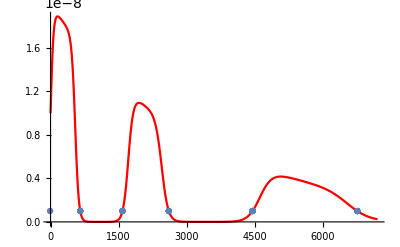

```mathematica
Show[Plot[a[t]/.sol,{t,0,tmax},PlotStyle->Red],ListPlot[{#,a[#]/.sol}&/@a1nms]]
```

## Computing with CRNs

### Analog rate-independent stoichiometric circuits that consume inputs (not taught this year -- skip this section)

The notion of computation here is that a CRN computes (x,y)=f(a,b) if when started with [A]_0=a, [B]_0=b, and everything else absent, the CRN will converge to [X]_∞=x, [Y]_∞=y, and maybe some other stuff left over; further this fact must hold for any set of positive rate constants assigned to the reactions.  It is a very strong requirement for robustness, and the types of functions computable with this constraint are in fact provably limited.  To the extent that computation can be done, it involves consuming and converting species from one form to another (hence “stoichiometric” -- how much gets converted to how much) until there is no more to convert.  (See e.g. “Deterministic function computation with chemical reaction networks” by Ho-Lin Chen, David Doty, and David Soloveichik, Natural Computing, 2014.)   We aren’t covering this case this year.  Feel free to poke around if you are curious.

Performing a well-defined amplification: size up to 2^kusing O(k) reactions.  Here, k=6.

```mathematica
rsys={rxn[a,2b,1], rxn[b,2c,1], rxn[c,2d,1],rxn[d,2e,1],rxn[e,2f,1],rxn[f,2g,1]}
```

{  a⟶^12 b,  b⟶^12 c,  c⟶^12 d,  d⟶^12 e,  e⟶^12 f,  f⟶^12 g}

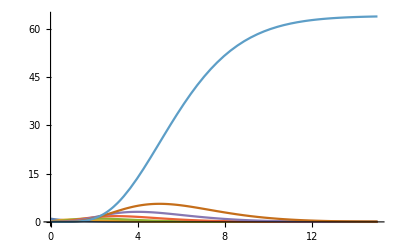

```mathematica
tmax=15;
sol=SimulateRxnsys[Join[rsys,{conc[a,1]}],tmax];
Plot[Evaluate[{a[t],b[t],c[t],d[t],e[t],f[t],g[t]}/.sol],{t,0,tmax},PlotRange->{0,All}]
```

```mathematica
g[tmax]/.sol
```

63.8213

How do we compute COPY, i.e. B_∞= C_∞=A_0 ? 

Note that the species C is represented by “c” because Mathematica has a built-in meaning for “C”. If you want to use uppercase “C”, note that C\[N u l l] is a different symbol, if typed without the spaces.

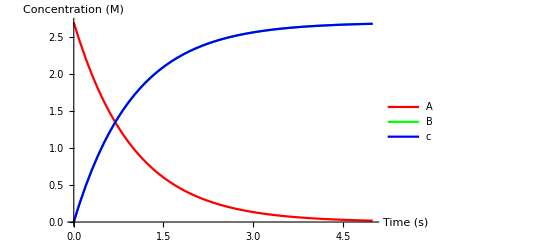

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A,B+c,1],conc[A,2.7]},tmax];
Plot[Evaluate[{A[t],B[t],c[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{B[tmax],c[tmax]}/.sol
```

{2.68181,2.68181}

How do we compute HALF, i.e. B_∞= 1/2 A_0 ?

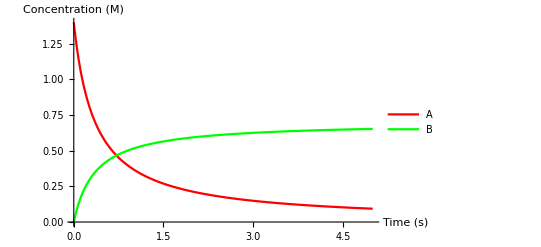

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A+A,B,1],conc[A,1.4]},tmax];
Plot[Evaluate[{A[t],B[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
B[tmax]/.sol
```

0.653333

How do we compute SUM, i.e. C_∞= A_0+B_0 ?

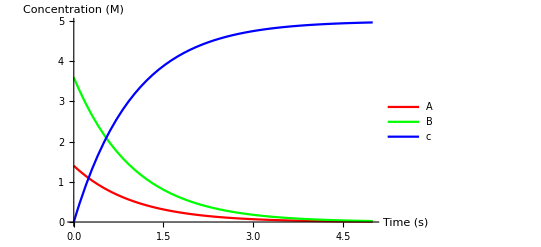

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A,c,1],rxn[B,c,1],conc[A,1.4],conc[B,3.6]},tmax];
Plot[Evaluate[{A[t],B[t],c[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
c[tmax]/.sol
```

3.59058

How do we compute MIN, i.e. C_∞= min(A_0,B_0) ?

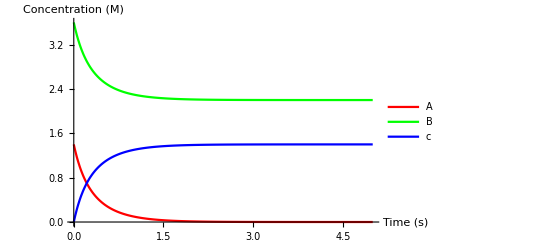

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A+B,c,1],conc[A,1.4],conc[B,3.6]},tmax];
Plot[Evaluate[{A[t],B[t],c[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
c[tmax]/.sol
```

3.59058

How do we compute MAX, i.e. C_∞= max(A_0,B_0) ?

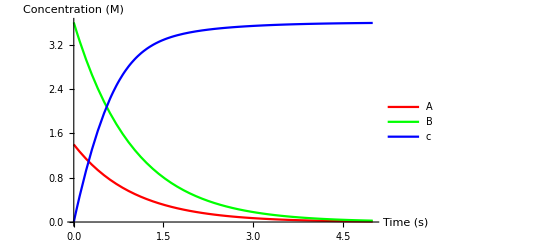

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A,c+P,1],rxn[B,c+Q,1],rxn[P+Q,X,1],rxn[X+c,0,1],conc[A,1.4],conc[B,3.6]},tmax];
Plot[Evaluate[{A[t],B[t],c[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{A,B,c},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
c[tmax]/.sol
```

Here we show the CRN implementation of a function that may have been discussed in the lecture:  Z_∞ = max(min(A_0,B_0), 1/2 A_0 + C_0).

This simulation time is such that the CRN hasn’t quite gone to completion yet, but is close.

```mathematica
rsys={
rxn[A,X+Y,1],
rxn[2X,P,1],
rxn[c,P,1],
rxn[Y+B,Q,1],
rxn[P,Z+R,1],
rxn[Q,Z+S,1],
rxn[R+S,T,1],
rxn[T+Z,0,1],
conc[A,5],conc[B,2],conc[c,3]
}
```

{  A⟶^1X+Y,  2 X⟶^1P,  c⟶^1P,  B+Y⟶^1Q,  P⟶^1R+Z,  Q⟶^1S+Z,  R+S⟶^1T,  T+Z⟶^10,conc[A,5],conc[B,2],conc[c,3]}

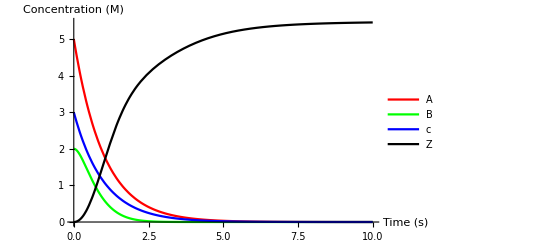

```mathematica
tmax=10;
sol=SimulateRxnsys[rsys,tmax];
Plot[Evaluate[{A[t],B[t],c[t],Z[t]}/.sol],{t,0,tmax},
PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue},{Black}},PlotLegends->{A,B,c,Z},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{Z[tmax],Max[Min[A[0],B[0]],A[0]/2+c[0]]}/.sol
```

Let’s show how easy it is to look at the input/output function for a CRN.  It would be more natural to just define rsys to have variables for the initial concentrations, but here we’re lazy and we just use an awkward rewriting rule to modify rsys to have the initial conditions we want -- which will be A between 0 and 5, B between 0 and 5, and C held constant at 1.  The accuracy is within 0.2 for this simulation time; presumably, an even longer simulation would get closer to the correct value.

```mathematica
io=Table[ (* build a 2D table, with each entry being the pair (simulation output, target function value) *)
sol=SimulateRxnsys[rsys/.{conc[A,5]->conc[A,A0],conc[B,2]->conc[B,B0],conc[c,3]->conc[c,1]},10*tmax];
{Z[tmax],Max[Min[A[0],B[0]],A[0]/2+c[0]]}/.sol,
{A0,0,5,0.1},{B0,0,5,0.1}];
simio = Map[First,io,{2}];
targetio = Map[Last,io,{2}];
```

```mathematica
{ListDensityPlot[simio,Mesh->None,InterpolationOrder->0,PlotLegends->Automatic],
ListDensityPlot[targetio,Mesh->None,InterpolationOrder->0,PlotLegends->Automatic]}
```

```mathematica
ListDensityPlot[simio-targetio,Mesh->None,InterpolationOrder->0,PlotLegends->Automatic]
```

```mathematica
Plot3D[Max[Min[A0,B0],A0/2+C0]/.C0->1,{A0,0,5},{B0,0,5},AxesLabel->{A0,B0,Z}]
```

### Rate-dependent analog computation by catalytic steady-state circuits (we ARE covering this!)

Relaxing the requirements that the long-term circuit behavior be independent of rate constants, as well as the requirement that all species other than the inputs are initially absent, leads us to a different notion of computation in CRNs.  Here, our convention will be that input species act catalytically to produce or degrade downstream species, so that the input concentrations are never changed, but the output species concentrations reach a steady-state.

How do we compute SQUARE, i.e. Z:= A^2 ?

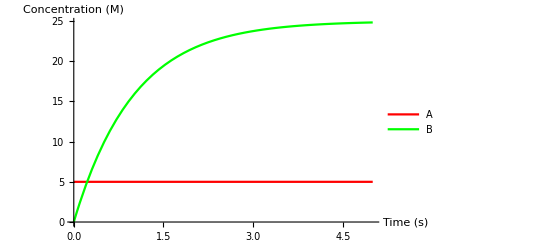

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A+A,A+A+B,1],rxn[B,0,1],conc[A,5]},tmax];
Plot[Evaluate[{A[t],B[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
B[tmax]/.sol
```

24.8316

How do we compute SQUAREROOT, i.e. Z:= √A ?

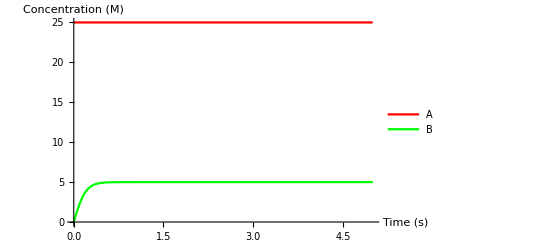

```mathematica
tmax=5;
sol=SimulateRxnsys[{rxn[A,A+B,1],rxn[B+B,0,1/2],conc[A,25]},tmax];
Plot[Evaluate[{A[t],B[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}},PlotLegends->{A,B},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
B[tmax]/.sol
```

An important feature of the CRNSimulator package is that it is possible to define CRN “subroutines” or “modules”, and systematically build larger CRNs based on those generic components.  Note that the H in CRNsub and the T in CRNam are instantiated as new unique variables (e.g. H$655 and T$78324) every time the module is used -- this way you can build a CRN that uses multiple “subtraction” (rsub) or “approximate majority” (am) modules with having their intermediate species interfere with each other.  Note that because the approximate majority (am) module changes the values of its inputs, it does not conform to the input/output convention discussed in class.  (Also, variable names don’t always agree with class notes.)

Here we demonstrate some of the modules from Vasic, Soloveichik, and Khurshid (2018), and apply them to compute the hypotenuse of a triangle according to the Pythagorean theorem, H = √(A^2+B^2).

```mathematica
CRNconst[A_,v_]:={rxn[0,A,v],rxn[A,0,1]}
CRNcopy[A_,B_]:= {rxn[A,A+B,1],rxn[B,0,1]}
CRNadd[A_,B_,C_]:={rxn[A,A+C,1],rxn[B,B+C,1],rxn[C,0,1]}
CRNsquare[A_,B_]:={rxn[2B,2B+A,1],rxn[A,0,1]}
CRNsqrt[A_,B_]:={rxn[A,A+B,1],rxn[B+B,0,1/2]}
CRNmul[A_,B_,C_]:={rxn[A+B,A+B+C,1],rxn[C,0,1]}
CRNdiv[A_,B_,C_]:={rxn[A,A+C,1],rxn[B+C,B,1]}
CRNrsub[A_,B_,C_]:=Module[{H},{rxn[A,A+C,1],rxn[B,B+H,1],rxn[C,0,1],rxn[C+H,0,1]}]
CRNam[A_,B_]:=Module[{T},{rxn[A+B,A+T,1],rxn[B+A,B+T,1],rxn[T+A,A+A,1],rxn[T+B,B+B,1]}]
```

```mathematica
rsys=Flatten[{CRNmul[A,A,A2],CRNmul[B,B,B2],CRNadd[A2,B2,S],CRNsqrt[S,H]}]
```

{  2 A⟶^12 A+A2,  A2⟶^10,  2 B⟶^12 B+B2,  B2⟶^10,  A2⟶^1A2+S,  B2⟶^1B2+S,  S⟶^10,  S⟶^1H+S,  2 H⟶^(1/2)0}

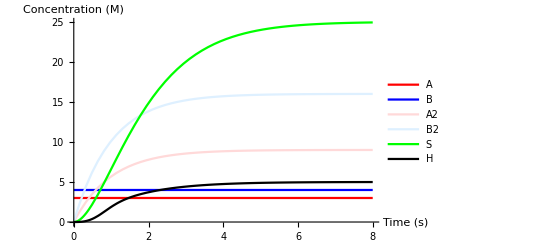

```mathematica
tmax=8;
sol=SimulateRxnsys[Join[rsys,{conc[A,3],conc[B,4]}],tmax];
Plot[Evaluate[{A[t],B[t],A2[t],B2[t],S[t],H[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{A,B,A2,B2,S,H},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

With these modules we can easily compute other functions as well, such as Y=X^2-√X+1.  Which of the following two implementations is correct, and why?

```mathematica
rsys=Flatten[{CRNsquare[X,SX],CRNsqrt[X,RX],CRNconst[c,1],CRNrsub[SX,RX,iX],CRNadd[iX,c,Y]}]
```

{  2 SX⟶^12 SX+X,  X⟶^10,  X⟶^1RX+X,  2 RX⟶^(1/2)0,  0⟶^1c,  c⟶^10,  SX⟶^1iX+SX,  RX⟶^1H$23455+RX,  iX⟶^10,  H$23455+iX⟶^10,  iX⟶^1iX+Y,  c⟶^1c+Y,  Y⟶^10}

```mathematica
rsys=Flatten[{CRNsquare[X,SX],CRNsqrt[X,RX],CRNconst[c,1],CRNadd[SX,c,iX],CRNrsub[iX,RX,Y]}]
```

{  2 SX⟶^12 SX+X,  X⟶^10,  X⟶^1RX+X,  2 RX⟶^(1/2)0,  0⟶^1c,  c⟶^10,  SX⟶^1iX+SX,  c⟶^1c+iX,  iX⟶^10,  iX⟶^1iX+Y,  RX⟶^1H$23719+RX,  Y⟶^10,  H$23719+Y⟶^10}

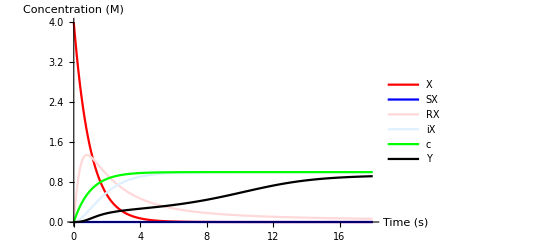

```mathematica
tmax=18;
sol=SimulateRxnsys[Join[rsys,{conc[X,4]}],tmax];
Plot[Evaluate[{X[t],SX[t],RX[t],iX[t],c[t],Y[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{X,SX,RX,iX,c,Y},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
inout=Table[tmax=100;sol=SimulateRxnsys[Join[rsys,{conc[X,x]}],tmax];{x,Y[tmax]/.sol},{x,0,2,0.1}];
```

```mathematica
Show[Plot[x^2-Sqrt[x]+1,{x,0,2}],ListPlot[inout]]
```

```mathematica
Plot[x^2-Sqrt[x],{x,0,2}]
```

### Example of adding/removing species during experiment (probably not to be used in lectures of homework for 2021)

Note: The examples below also require CRNSimulatorExtensions.m to be loaded and run.

```mathematica
Get["CRNSimulatorExtensions.m"]
```

```mathematica
rsys={
revrxn[a+b,c,0.1,30],
rxn[2a,b,0.01],
conc[c,1]
};
```

Our interest here is to see how a CRN responds to input that is given at various times, not just as the initial conditions.

We don’t specify the initial concentrations of a, b because these are controlled by a schedule. Positive numbers means add this amount, negative numbers means remove this amount. The first column is the time to wait until next addition.  The remaining columns indicate the amounts to add (or remove) for the respective species listed in the SimulateRxnsysWithSchedule[ ] call.

```mathematica
schedule={
{10,0,0},
{50,4,0},
{20,0,10},
{20,10,0},
{20,0,-9},
{20,-2,0}
};
```

```mathematica
SpeciesInRxnsys[rsys]
```

```mathematica
tmax=Total[schedule⟦All,1⟧]
```

```mathematica
sol=SimulateRxnsysWithSchedule[rsys,schedule,{a,b}];
```

```mathematica
plotter={a[t],b[t],c[t]}/.sol;
```

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}}]
```

### Example of providing an external input

You might not want to provide discrete pulse inputs, but rather set a time-varying concentration.

You can intermix definitions of the form x[t]==..., x’[t]==..., with rxn, term, and conc statements.

```mathematica
tmax=20;
```

```mathematica
rsys={
u[t]==0.1 Sin[t]+1,
revrxn[x1+u,x2,1,1],
conc[x1,1]
};
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotter={x1[t],x2[t],u[t]}/.sol;
```

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->All]
```

### Some relevant references

Vasić, Marko, David Soloveichik, and Sarfraz Khurshid. “CRN++: Molecular programming language.” Natural Computing 19, no. 2 (2020): 391-407.
Fages, François, Guillaume Le Guludec, Olivier Bournez, and Amaury Pouly. “Strong Turing completeness of continuous chemical reaction networks and compilation of mixed analog-digital programs.” In International conference on computational methods in systems biology, pp. 108-127. Springer, Cham, 2017.
Huang, Xiang, Titus H. Klinge, and James I. Lathrop. “Real-Time Equivalence of Chemical Reaction Networks and Analog Computers.” In International Conference on DNA Computing and Molecular Programming, pp. 37-53. Springer, Cham, 2019.
Salehi, Sayed Ahmad, Keshab K. Parhi, and Marc D. Riedel. “Chemical reaction networks for computing polynomials.” ACS synthetic biology 6, no. 1 (2017): 76-83.